# Programming: Wolfram Language and Mathematica Fundamentals

```mathematica
-Graphics--Graphics-
```

Both Mathematica and the Wolfram Language are developed and owned by the commercial entity Wolfram Research - the use of both these technologies are subject to their licensing and EULA agreements.

Mathematica is a powerful IDE for using the Wolfram Language to investigate, analyse and visualise data. It is fairly unique in that the UI is generated from intepreted Wolfram Language code and may also be programmatically manipulated using the Wolfram Language.

In general, most users of the Wolfram Language use the Mathematica interface (called the notebook) as it provides a literate programming environment. As we’ll see throught this course, it’s possible to create interactive visualisations within Mathematica notebooks and to share these with others using a variety of technologies that are discussed in the Wolfram Cloud section of this course.

It is possible to use the Wolfram Language through the shell, on a server or remotely on the cloud - this course only considers the desktop Mathematica environment in detail.

# What is this course about?

This course introduces the Wolfram Language and the Mathematica environment from the point of view of an user interested (or experienced) in computer programming and the processing or simulation of research data.

In this course we do not consider the very powerful visualisation and interactive capabilities of the Wolfram Language, a dedicated course called Data Analysis & Creating Interactive Visualisations with Mathematica provides an overview of this.

This course also does not cover the diverse analytical capabilities of the Wolfram Language, for instance its network analysis, machine learning, or analytical calculus functions. Future ITLP course may concentrate on these features if there is sufficient interest.

# Why use the Wolfram Language?

The Wolfram Language is an example of a scripting language, for our purposes a scripting language is defined as follows:

Scripting languages allow users to write code that automate tasks in a “read-eval-print” loop, do not require a deep understanding of computer science and typically provide a wide array of libraries of built-in functions for performing complex operations in a simple way. Often without understanding the specifics of the alogorithm or underlying mathematica principles.

Scripting languages include:

Python

R

Wolfram Language

## Symbolic Computation

The Wolfram Language is fairly unique in the scripting languages in that it was originally designed for solving calculus and algebraic problems.

It is therefore often described as a symbolic language which provides two benefits to all users

Mathematical problems can be solved directly and simply

```mathematica
Solve[{4*x^2+x+2==0},x]
```

Output can be represented symbolically, allowing the user to understand how expressions are evaluated

```mathematica
NestList[#+b^#&,1,3]
```

Other scripting languages have a broad community of users who contribute small, dedicated packages/libraries for specific functionality, for instance in R there is library called lubridate that is incredibly useful for handling dates.

In the case of the Wolfram Language, the vast majority of functionality is developed by Wolfram Research and built into the product. This is often an advantage as functions work together seemlessly and handle multiple data types, however there is a disadvantage in the inner workings of functions often being unavailable to the end user.

```mathematica
digit=Classify[
{-Graphics-->2,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->2,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->9,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->2,-Graphics-->0,-Graphics-->6,-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->7,-Graphics-->8,-Graphics-->5,-Graphics-->0,-Graphics-->4,-Graphics-->7,-Graphics-->6,-Graphics-->0,-Graphics-->2,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->4,-Graphics-->1,-Graphics-->9,-Graphics-->3,-Graphics-->6,-Graphics-->8,-Graphics-->0,-Graphics-->9,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->7,-Graphics-->4,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->0,-Graphics-->4,-Graphics-->1,-Graphics-->3,-Graphics-->7,-Graphics-->6,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->7,-Graphics-->2,-Graphics-->5,-Graphics-->2,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->9,-Graphics-->8,-Graphics-->1,-Graphics-->6,-Graphics-->4,-Graphics-->8,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->6,-Graphics-->7,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->1,-Graphics-->9,-Graphics-->9,-Graphics-->9,-Graphics-->2,-Graphics-->4,-Graphics-->7,-Graphics-->3,-Graphics-->1,-Graphics-->9,-Graphics-->2,-Graphics-->9,-Graphics-->6}];
digit[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,1,2,3,4,1,4,7,8,9}

This course will not explore these capabilities or further compare the Wolfram Language to other scripting languages. However it is useful to understand from the outset of learning a language what it is useful for and how it differs from other languages.

## Programming Paradigms

In addition to the unusualness of orignally being designed for solving symbolic problems, the Wolfram Language has incubted within a Computer Algebra System since 1987 and is heavily influenced by functional languages popular in the 80s and previous decades. The language therefore provides a variety of unusual paradigms for solving problems.

Take for instance a fairly standard introductory programming task:

How would you write a program to sum to perform the following transformation:

(58 | 96
85 | 22
100 | 69
5 | 37
32 | 64
41 | 86
14 | 0
79 | 22
3 | 5) | ⟹ | (154
107
169
42
96
127
14
101
8)

The input is a two column array, the output of the program is a single column array containing the sum of each row. In the Wolfram Language there are at least three fundamentally different approaches to this problem.

### Procedural Programming

The traditional approach to this problem is to construct a loop that will operate on the array and populate an initially empty array (or partwise modify an existant array) with the summation of each row.

```mathematica
matrix={{58,96},{85,22},{100,69},{5,37},{32,64},{41,86},{14,0},{79,22},{3,5}};
```

```mathematica
result=ConstantArray[Null,Length[matrix]];
Do[
result[[k]]=Total[matrix[[k]]],
{k,1,Length[matrix]}
]
result
```

Loops require an understanding of side affects and require operations to be abstracted which can be tremendously useful (particularly for complex probems) but may be difficult for non-programmers to understand. It should also be noted that due to the nature of the Wolfram Language’s internal pattern replacement mechanic and interpretation levels, loops are often not the most efficient approach to solving a problem

However, note that while this course does not deeply consider how to write efficient code there are a number of sign posts provided to the beginner to encourage good standards.

### Rule-Based Programming

```mathematica
matrix1={{58,96},{85,22},{100,69},{5,37},{32,64},{41,86},{14,0},{79,22},{3,5}};
```

lhs /. rhs replaces every element on the lhs that matches the conditional pattern on the rhs according to the specified rule. ReplaceAll is the FullForm of /. but is hardly ever used.

```mathematica
matrix1/.{p_,q_}->p+q
```

### Functional

Mathematica has a huge number of built-in functions that are often more efficient and easier to use than procedural or rule-based programming.

### Comparison

Pushing for as much efficiency as possible in each approach, a functional approach still beats the others by more than an order of magnitude. Functional programming within the Wolfram Language provides potentially novel and fast solutions to problems you might otherwise write as complex loops.

```mathematica
matrix=RandomReal[1,{40000,2}];
doloop$timing=RepeatedTiming[
doloop=ConstantArray[0,Length[matrix]];
Do[doloop[[k]]=
Total[matrix[[k]]],
{k,1,Length[matrix]}]
];
rules$timing=RepeatedTiming[rules=matrix/.{p_,q_}->p+q;];
functional$timing=RepeatedTiming[Total[Transpose[matrix]];];
```

```mathematica
Grid[Prepend[Transpose@{{"Procedural Loop","Rule Replacement","Functional"},1000*{doloop$timing,rules$timing,functional$timing}[[All,1]]},{"Approach","Timing (milliseconds)"}],Frame->All,BaseStyle->"Text"]
```

Approach | Timing (milliseconds)
Procedural Loop | 92.
Rule Replacement | 36.
Functional | 1.4

# Five Things You Need to Know

To use the Mathematica environment there are five things you need to know:

## Cells

Content in Mathematica notebooks is arranged is Cells - the cell brackets to the right of content are used to select cells and cell groups.

When a new notebook is opened there is a flashing horizontal cursor indicating the cursor placement, if you type then content will be entered into a new cell.

Cells have different styles. By default, new cells are Input Cells - where Wolfram Language code is written. As an example, type Hello World

This input will be interpreted as the multiplication of two symbols: hello×world.

The style of a cell can be modified in a number of ways:

Right-click the cell bracket and select Style

Select the cell bracket and select Format→Style from the menubar

```mathematica
-Graphics--Graphics-
```

Selecting the style Title will format your input according to the stylesheet’s definition of Title.

Notice that as the cursor moves around a notebook it changes state - a vertical cursor indicates the cursor is within a cell and clicking will select the contents of that cell. A horizontal cursor indicates that you are between cells, clicking will provide the cell insertion bar (or I-beam) which will allow the creation of a new cell.

## Shift+Enter to Evaluate

Shift+Enter is used to evaluate an input cell, to demonstrate this type Hello World into a new cell and hit Shift+Enter. There are three things to note:

-Graphics-

Output is printed in a new cell - which is grouped together with the Input Cell. Both these input and output cells are grouped together with the Title Cell above.

The input and output cells are labelled In[1] and Out[1] - it is important to understand that the labelling is temporal and not spatial.

The Suggestions Bar is displayed underneath output cells and suggests a number of operations that may be performed on the ouput

Shift+Enter is how all code evaluated, it is the most important keyboard shortcut to remember in Mathematica.

It is recommended that different styled cells are used to write prose, to include comments in code chunks the syntax is (*these are comments*)

-Graphics-

Cell groups can be collapsed and opened by double-clicking on cell brackets.

## CamelCase

There are over 5000 symbols defined in the Wolfram Language, all of these are written in CamelCase. All built-in symbols start with a capital letter and each sub-word does as well, this allows for easy function discovery and auto-completion.

All charting functions can be discovered using the following syntax:

```mathematica
?*Chart*
```

It is highly recommended that all user-defined symbols are written in bowingCamelCase so as to distinguish between built-in and user-defined symbils.

## Command Completion

Symbols that are blue are unknown to Mathematica (they have no definition), both user-defined and built-in symbols with definitions are coloured black:

```mathematica
BarChart
```

When a symbol name is complete the following shortcuts can be used to obtain a template for the function: ⌘+⇧+K (Mac) and Ctrl+⇧+K (Windows)

## F1 for Help

The Wolfram Documentation uses the literate programming paradigm provided by the notebook interface to provide an amazing wealth of examples and documentation for most built in symbols.

To obtain the documentation page for a symbol, simply select the symbol and press F1.

# Brackets and Writing Code in the Wolfram Language

The Wolfram Language is a highly bracketed language, to read other’s code and to minimise errors it’s important to understand what brackets mean.

RandomInteger is a tremendously useful function for introducing this:

```mathematica
RandomInteger[{1,(1+2)*2},{2,2}]
```

{{4,3},{5,5}}

Square brackets [[ ]] contain function arguments

Round brackets are used to control precedence of operations

Curly brackets (braces) are used to denote Lists (vectors, in other languages)

## Alternative Forms of Expressions

Because of the heavily bracketed nature of the language, it is often convenient to use alternative forms of a function - it is important that you’re introduced to these in a programming course as other’s code will almost undoubtably use these patterns.

```mathematica
Total[{1,2,a,4}]
```

7+a

Postfix allows a function to be applied to the preceeding expression

```mathematica
{1,2,a,4}//Total
```

7+a

Prefix allows a function to be applied to the beginning of an expression

```mathematica
Total@{1,2,a,4}
```

7+a

# Writing Functions in the Wolfram Language

This course primarily considers how data may be generated within Mathematica, rather than through the importation of an existent dataset in an Excel file. To provide a useful introduction to the syntax for writing user-defined functions let us consider how to write a program that will achieve the following:

Generate random integers → Calculate a running total → Visualise the output in a ListPlot

The individual steps are simply achieved:

Assign the output of RandomInteger to the symbol numbers:

```mathematica
numbers=RandomInteger[10,10]
```

{9,1,8,7,3,4,3,0,4,8}

Use the function Accumulate to compute the running total of numbers:

```mathematica
runningTotal=Accumulate[numbers]
```

{9,10,18,25,28,32,35,35,39,47}

ListPlot is used for visualising univariate and bivariate datasets, it’s therefore used for creating scatterplots:

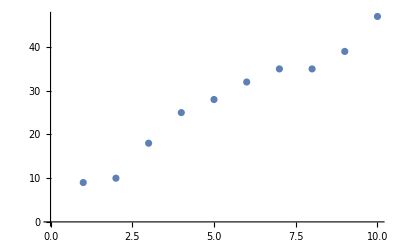

```mathematica
ListPlot[runningTotal]
```

## Notes on Symbol Definitions

It is generally good practice to use kneelingCamelCase for user-defined functions so as not to conflict with system defined symbols.

The assigning of variables in the Wolfram Language is another case where an alternatve form of an expression is used, the following input is identical. The = character is the infix notation for the function Set.

```mathematica
Set[numbers,RandomInteger[10,10]]
```

```mathematica
numbers=RandomInteger[10,10]
```

Whenever describing these assignments we say “set a as b”

## User defined functions

The steps above can be combined together into one expression:

```mathematica
ListPlot[Accumulate[RandomInteger[10,10]]]
```

The following defines a function allowing for repeatable use of this script:

```mathematica
accumulatePlot[n_]:=ListPlot[Accumulate[RandomInteger[10,n]]]
```

As with the previous type of assignment, this is the infix notation for a function:

```mathematica
SetDelayed[
accumulatePlot[Pattern[n,_]],
ListPlot[Accumulate[RandomInteger[10,n]]]]
```

The FullForm of SetDelayed is almost never used but exposes the pattern matching nature of the Wolfram Language, the language used to describe this is “we define the function accumulatePlot.... “

Below are three function definitions with unique pattern restrictions on the first argument:

This function will only evaluate if provided with a single argument that is a string:

```mathematica
func1[var1_String]:=StringJoin[var1," was a string"]
```

This function will only evaluate if provided with a single argument that is an integer:

```mathematica
func2[x_Integer]:=RandomInteger[10,x]
```

This function will only evaluate if provided with a single argument that is greater than 1

```mathematica
func3[max_/;max>1]:=RandomReal[max,10]
```

To understand this behaviour it is necessary to expose the underlying nature of expressions in the Wolfram Language - all expressions have a Head

```mathematica
Head["quick brown fox"]
```

```mathematica
Head[1]
```

```mathematica
Head[1.]
```

This concept is key to understanding how function definitions, pattern matching and replacment rules work in the Wolfram Language.

# Exercises: Rewriting Expressions and Functions

## Rewriting Expressions

Correct the following expressions:

```mathematica
barFunc(list_,labels):=BarChart[list,ChartLabels->labels]
```

```mathematica
(1,2,3)+{a,b,c}
```

```mathematica
DeleteStopwords(["this","that","course","and","more","besides"}]
```

## Moving Average

Follow these steps to create a function that will achieve the following:

generate random variates → calculate a moving average → plot the moving average using ListPlot

HINT: If you make a mistake with your function definition you may wish to inspect the following lines:

```mathematica
removeMe[x_]:=x^2
removeMe[2]
```

```mathematica
Remove[removeMe];
removeMe[x_/;x>10]:=x^2
removeMe[2]
```

Look up the documentation for RandomVariate and write a script for generating n random numbers from a NormalDistribution with a mean and standard deviation of your choosing.

Use the function MovingAverage to compute the moving average of the list, with runs of length 2

Use the function Accumulate to compute a running total of this output

Show the output of step 3 using ListPlot

Combine steps 1-4 to create a function called movingAveragePlot with the following arguments:

number of variates generated from NormalDistribution

the size of the runs used in MovingAverage

Prevent the function from evaluating if the following conditions are NOT met:

the number of variates is an Integer

the number of variates is greater than twice the run size used in MovingAverage

## RandomReal

There is a fundamental difference between the two following assignments:

```mathematica
set$Random=RandomInteger[{1,10}]
```

```mathematica
setDelayed$Random:=RandomInteger[{1,10}]
```

Explain why the output of the following expression changes each time it is evaluated:

```mathematica
Table[ListLinePlot[RandomInteger[set$Random,setDelayed$Random]],5]
```

# Data Structures: Lists

The Wolfram Language includes a number of useful example datasets, similar to other scripting languages. These can be accessed using the ExampleData function:

```mathematica
ExampleData["Statistics"]
```

For a broadly interesting example, the following example from econometrics will be used:

```mathematica
ExampleData[{"Statistics","EmployeeAttitude"}]//Short
```

{{43,51,30,39,61,92,45},«28»,{82,82,39,59,64,78,39}}

As with many functions in the Wolfram Language, additional information (or meta-information) can be assessed with the string argument, “Properties”

```mathematica
ExampleData[{"Statistics","EmployeeAttitude"},"Properties"]
```

{ApplicationAreas,ColumnDescriptions,ColumnHeadings,ColumnTypes,DataElements,DataType,Description,Dimensions,EventData,EventSeries,LongDescription,Name,ObservationCount,Source,TimeSeries}

The source for this data can be returned as follows:

```mathematica
ExampleData[{"Statistics","EmployeeAttitude"},"Source"]
```

Chatterjee, S. and Price, B. (1977) Regression Analysis by Example. New York: Wiley. (Section 3.7, p.68ff of 2nd ed.(1991).)

For the purposes of an example, extract the data and column headings for the dataset as follows, note the use of $ within a symbol name to specify distinct components of the dataset.

In R the $ operator is used for adding columns to data.frame, in the WL there is no consequence for using the $ in the symbol name.

```mathematica
attitudes$Data=ExampleData[{"Statistics","EmployeeAttitude"}];
attitudes$Headings=ExampleData[{"Statistics","EmployeeAttitude"},"ColumnHeadings"];
```

To preview the data before introducing Parts it is useful to use Grid, note the use of an Option to control the output of the expression.

```mathematica
Grid[Prepend[attitudes$Data,attitudes$Headings][[;;5]],Frame->All]
```

Rating | Complaints | Privileges | Learning | Raises | Critical | Advancement
43 | 51 | 30 | 39 | 61 | 92 | 45
63 | 64 | 51 | 54 | 63 | 73 | 47
71 | 70 | 68 | 69 | 76 | 86 | 48
61 | 63 | 45 | 47 | 54 | 84 | 35

## Lists

In the section on function definitions the concept of a Head was introduced, the Head of the data structures used here is List.

```mathematica
Head[attitudes$Data]
```

List

Lists are the most broadly used data structure in the Wolfram Language, and were the only data structure save for highly optimised arrays before 2013.

## Extracting Parts from Lists

In the Wolfram Language the n-th element of a list is the n-th element of a list, and can be extracted using the function Part:

```mathematica
Part[attitudes$Data,1]
```

This is more typically written in shorthand:

```mathematica
attitudes$Data[[1]]
```

It is often convenient to extract elements by negative index:

```mathematica
attitudes$Data[[-1]]
```

Nested lists may be difficult to interpret by eye, it can therefore be useful to use MatrixForm to visualise the data as a matrix:

```mathematica
MatrixForm[attitudes$Data]
```

When using Part it is useful to remember that the Wolfram Language is (at least in general) row orientated - so to extract the second column of the third element of departmentsTally the following would be evaluated:

```mathematica
attitudes$Data[[3,2]]
```

2

To extract the entirety of the second column it is therefore necessary to use the operator All

```mathematica
attitudes$Data[[All,2]]
```

{3,2,2,1,1}

# Data Structures: Associations

Lists are the most widely used data structure in the Wolfram Language, most functions output their results in Lists for instance:

```mathematica
Solve[x^2+1==0,x]
```

{{x→-ⅈ},{x→ⅈ}}

However, it is only possible to access elements of a list by their index - making it difficult to operate on data structures like the example dataset we are considering, it would be tremendously useful to be able to extract these elements by their column names.

This is achieved in programming languages through the use of an associative array, typically through the use of “key, value” pairs.

In the Wolfram Language these are called Associations and have the following syntax:

```mathematica
assoc=<|"Category"->"A","Size"->10,"Users"->1021,"Interactions"->12|>
```

<|Category→A,Size→10,Users→1021,Interactions→12|>

## Lists of Associations

Associations are primarily useful when there is a collection of them, a List of Associations.

```mathematica
assocs={
<|"Category"->"A","Size"->10,"Users"->1021,"Interactions"->12|>,
<|"Category"->"B","Size"->12,"Users"->1121,"Interactions"->120|>};
assocs[[All,"Category"]]
```

{A,B}

Programmatically constructing Associations is most easily achieved through the use of AssociationThread - the threading of two lists together is a functional paradigm quite common to the Wolfram Language.

```mathematica
newAssoc=AssociationThread[{"Key 1","Key2","Other Key"},{1,2,5}]
```

<|Key 1→1,Key2→2,Other Key→5|>

There are a multitude of functions for creating expressions - which will be covered and compared in detail later, for now let us consider the function Table.

```mathematica
columnNames={"Key 1","Key2","Other Key"};
data=RandomInteger[5,{5,3}];
```

```mathematica
Table[AssociationThread[columnNames->data[[i]]],{i,Length[data]}]
```

{<|Key 1→2,Key2→5,Other Key→2|>,<|Key 1→2,Key2→1,Other Key→3|>,<|Key 1→3,Key2→5,Other Key→2|>,<|Key 1→3,Key2→0,Other Key→0|>,<|Key 1→4,Key2→3,Other Key→5|>}

## Dataset

Dataset is a data structure currently under development within the Wolfram Language for storing both Lists and Associations. There are potentially very useful applications of the data structure thanks to its ability to handle non-rectangular data structures.

```mathematica
dataset=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z"|>}]
```

a | b | c
1 | x | { 1 }
2 | y | { 2,3 }
3 | z | { 3 }
4 | x | { 4,5 }
5 | y | { 5,6,7 }
6 | z | KeyAbsent
3 levels | 6rows |  | Dataset[{__Association}]

While the data structure has been integrated into the language and is documented, it is currently is not supported widely by the system and has some quirks. Future development of a type system for the Wolfram Language, and out-of-memory data processing will make Dataset a tremendously useful tool.

This course does not cover Dataset in any further detail, it is sufficient to consider a Dataset as a List of Associations and to use the same Query operators as for such objects. You are advised that if you use Dataset at present there will be many situations where the object must be converted into a List of Associations - this is achieved with Normal:

```mathematica
Normal@dataset
```

{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{3}|>,<|a→4,b→x,c→{4,5}|>,<|a→5,b→y,c→{5,6,7}|>,<|a→6,b→z|>}

## Querying Associations

The pattern matching capabilities of the language makes it fairly easy to extract elements of a list based on patterns and conditions.
The Cases function is particularly useful for this, note that the syntax is fundamentally identical to that used previously when defining input-restricted functions:

```mathematica
data1={{1,"UK",34,"string"},{6,"US",45,0}};
Cases[
data1,
{_,_,age_,value_String}/;age>30]
```

Data is extracted from Associations through the use of Queries, via the function Query. 

The arguments of Query should be considered as operators that are sequentially applied to a data structure (such as a list of associations), for this reason Query is typically applied using the Prefix operator. In the following Query, the total of all values for the key “Other Key” is returned:

```mathematica
assocs={<|"Key 1"->2,"Key2"->1,"Other Key"->0|>,<|"Key 1"->5,"Key2"->1,"Other Key"->4|>,<|"Key 1"->4,"Key2"->5,"Other Key"->2|>,<|"Key 1"->0,"Key2"->3,"Other Key"->5|>,<|"Key 1"->1,"Key2"->3,"Other Key"->2|>};
```

```mathematica
Query[Total,"Other Key"]@assocs
```

To select elements from the data structure according to their value it is necessary to use an anonymous function. Anonymous functions do not have named arguments, they use the Slot Operator (shorthand: #)

```mathematica
Function[x,x^2+1][10]
```

```mathematica
Slot[]^2+1&[10]
```

101

```mathematica
#^2+1&[10]
```

When querying associations, it’s possible to use named slots:

```mathematica
Query[Select[Slot["Key 1"]==2&]]@assocs
```

```mathematica
Query[Select[#"Key 1" == 2 & ]][assocs]
```

# Exercises

## RandomVariates, Cases and Pattern Replacements

This question recaps function definitions, introduces RandomVariate and Cases.

Refer to the documentation for RandomVariate and write a function to generate n random variates from a normal distribution with mean m and standard deviation sd

The function should, when given the following input return a list containing 10 elements from a normal distributiin with mean 0 and standard deviation 1

```mathematica
yourFunction[10,0,1]
```

Use the function Cases to return all elements that are less than zero

Cases is only useful for returning elements. The Position function could be used to find the relative positions of offending elements and replace them, but this is inefficient.

Replacement rules use the same pattern matching syntax already introduced, use the following examples to answer the questions below (remember that selecting an expression you don’t recognise and pressing F1 will bring up the documentation)

```mathematica
{"a","aa","bb","c","ccc"}/.a_String/;StringLength[a]>1->"long string"
```

```mathematica
ReplaceAll[{"a","aa","bb","c","ccc"},a_String/;StringLength[a]>1->"long string"]
```

{a,long string,long string,c,long string}

Use the ReplaceAll function to replace all values less than 0 with 0

## Rows and Columns with Parts

This course does not deeply consider the importation or processing of data, however the following template is provided for your benefit as well as to load data for the this exercises:

Set the working directory using SetDirectory

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop","Exercises"}]]
```

List Files

```mathematica
FileNames[]
```

Import the .csv file

```mathematica
csvimport=Import["small-csv.csv","CSV"];
```

The dataset is quite small:

```mathematica
Grid[csvimport]
```

Name | Age | City of Birth
Jane | 23 | Northampton
Sally | 21 | Bellyinborough
Rita | 25 | Budapest
Louis | 26 | Edinborough
James | 22 | Edinborough
Judy | 26 | Cardiff
Rowan | 28 | Budapest
Mike | 29 | Edinborough
Meriel | 28 | Edinborough
Kevin | 23 | Northampton
Ken | 25 | Budapest
Howard | 26 | Budapest

Use Part (shorthand or longhand) to extract the city of birth column

Use the function Tally to tally the frequency of cities of birth - assigning the data structure to an appropriate variable

Use Part to extract the counts from the Tally to create the following BarChart - make sure there are only as many bars as there are distinct cities

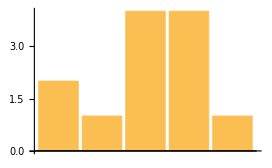

Optional steps to make a useful visualisation, skip to the next question if you would prefer to focus on the programming concepts introduced here.

Use the Options ChartLabels and BarOrigin to produce the following chart:

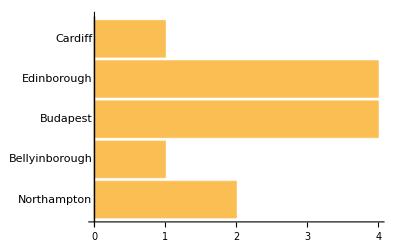

Sort the Tally such that the city(ies) with the largest counts are shown first using SortBy

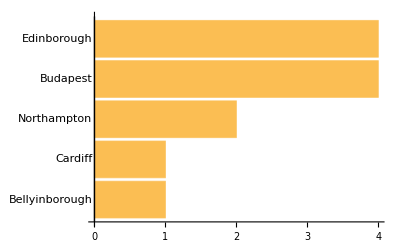

## Creating Associations with Table

Use Table to convert the data from this dataset into an association:

```mathematica
ExampleData[{"Statistics","SwissBankNotes"}]
```

Extract the ColumnHeadings and data from ExampleData and assign to appropriate symbols

Use the pattern introduced by the lecturer for converting this data into a list of associations through the following functions:

Table

AssociationThread

## Anonymous Functions

Anonymous functions are extremely useful in the Wolfram Language and are used frequently in code that you’ll find on StackExchange and other resources.

They’re also necessary for performing queries on associations.

Convert the function definition below into a pure function and provide it the argument “ ”

```mathematica
function[a_]:=Riffle[{"You","will","find","this","function","useful"},a]
```

Pure functions are useful in nesting functions

```mathematica
NestList[(1+#)^2&,x,3]
```

Modify the above function such that it calculates compound interest for a savings account with the following details:

Initial balance of 1000

Annual interest rate of 30%

Three year no-withdrawal (or deposit) limit

## Querying Associations

If you have succesfully created an association for the SwissBankNotes dataset then use that for this question, otherwise here is a sample of the data:

```mathematica
swissBankNotes={<|"Length"->214.8,"Left"->131,"Right"->131.1,"Bottom"->9,"Top"->9.7,"Diagonal"->141,"Counterfeit"->0|>,<|"Length"->214.6,"Left"->129.7,"Right"->129.7,"Bottom"->8.1,"Top"->9.5,"Diagonal"->141.7,"Counterfeit"->0|>,<|"Length"->214.8,"Left"->129.7,"Right"->129.7,"Bottom"->8.7,"Top"->9.6,"Diagonal"->142.2,"Counterfeit"->0|>,
<|"Length"->215.1,"Left"->129.5,"Right"->129.6,"Bottom"->7.7,"Top"->10.5,"Diagonal"->142.2,"Counterfeit"->0|>,<|"Length"->215.2,"Left"->130.8,"Right"->129.6,"Bottom"->7.9,"Top"->10.8,"Diagonal"->141.4,"Counterfeit"->0|>,<|"Length"->215.5,"Left"->130.4,"Right"->130,"Bottom"->8.2,"Top"->11.2,"Diagonal"->139.2,"Counterfeit"->1|>,<|"Length"->214.7,"Left"->130.6,"Right"->130.1,"Bottom"->11.8,"Top"->10.5,"Diagonal"->139.8,"Counterfeit"->1|>,<|"Length"->214.7,"Left"->130.4,"Right"->130.1,"Bottom"->12.1,"Top"->10.4,"Diagonal"->139.9,"Counterfeit"->1|>,<|"Length"->214.8,"Left"->130.5,"Right"->130.2,"Bottom"->11,"Top"->11,"Diagonal"->140,"Counterfeit"->1|>};
```

Extract the lengths of counterfeit and non-counterfeit bank notes

Calculate the mean of these two dataset - how different are they?

Recalling that “Properties” is a useful way to explore objects, first extract the test conclusion from the object below and then use this pattern to test whether the counterfeit and non-counterfeit bank notes could be differentiated based on their length.

```mathematica
ttest=TTest[{{13,10,10,11,4},{12,5,4,5,2}},Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

How direct (minimal number of steps) a query can you build to find the mean length of counterfeit notes?

# Constructing Expressions

The construction of expressions (and data structures) helps us expose a variety of features of the language and the use of Mathematica.

We’ll consider the following topics:

RandomReal, ConstantArray and SparseArray

Table and ParallelTable

Map and Anonymous Functions

Loops

## RandomReal and ConstantArray

Monte Carlo simulations in most languages are typically written in terms of For loops that operate on an initially empty array, given the current topics we’ve covered it might make sense to use RandomReal to generate an all-zero array:

```mathematica
emptyArray=RandomReal[0,{100,100}];
```

However, this is surprisingly slow for only moderately large arrays. To time how long an evaluation takes use the function AbsoluteTiming, note that the output of the function is a list with the following structure: {timing, output}

```mathematica
{timing$RandomReal,emptyArray$RandomReal}=AbsoluteTiming[RandomReal[0,{10000,10000}]];
timing$RandomReal
```

1.2791

The Wolfram Language has over 5,000 built-in functions and often has a built in function for solving common programming tasks, such as creating constant arrays:

```mathematica
{timing$ConstantArray,emptyArray$ConstantArray}=AbsoluteTiming[ConstantArray[0.,{10000,10000}]];
```

Individual elements of the array can now be updated using peicewise assignments:

```mathematica
emptyArray$ConstantArray[[1,10]]=1.
```

Note that it is important to keep the Head of elements in a ConstantArray the same, this allows for a Wolfram Language system to keep the internal representation of your object as an efficiently stored PackedArray. For more details about PackedArray please refer to the documentation.

## Table and Parallelisation

Table is extremely useful for generating expressions, it is essentially an efficiently implemented Do loop with a print statement. Code written in other languages as Do loops can typically be more efficiently implemented in the Wolfram Language through the use of Table.

```mathematica
Table[Plot3D[Sin[x+y]^n,{x,-2Pi,2Pi},{y,-2Pi,2Pi},ImageSize->Tiny],{n,1,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Table can easily be parallelised through the use of ParallelTable, note that this example is from the Wolfram Documentation and demonstrates functionality outside of the scope of this introductory course to the language. 

However, the example demonstrates well that Table, and it’s parallelised sibling, should be considered whenever generating output for consumption by other functions - including graphical output.

```mathematica
eqn=D[z[t,s],t,t]==-z[t,s]/((z[t,s]^2+(1/2 (1+0.1 Sin[2 Pi t]))^2)^(3/2));
sols=ParallelTable[localsol=NDSolve[{eqn,z[0,s]==param s,Derivative[1,0][z][0,s]==param},z,{t,0,10}, {s,1,2}]; 
Plot3D[Evaluate[z[tp, z0]/.localsol],{tp,0,10},{z0,1,2},PlotRange->{-5,5},PlotLabel->param], 
{param, -1,1,0.1}];
ListAnimate[sols]
```

## Map and its cousins

Map (and its cousins) are tremendously useful operations for generating expressions, however they require an understanding of anonymous (or pure) functions. 

Note that Map similar to the lapply function found in R.

In the example below an anonymous function is mapped over List[a,b,3,4]:

```mathematica
Map[#^2+1&,{a,b,3,4}]
```

{1+a^2,1+b^2,10,17}

Map is used frequently enough that that is a shorthand for it:

```mathematica
#^2+1&/@{a,b,3,4}
```

### Properties with Map

For a practical application of Map it is useful to reconsider a previous example:

```mathematica
ExampleData[{"Statistics","EmployeeAttitude"},"Properties"]
```

Another object with properties is the output of *ModelFit functions:

```mathematica
data={1,3,6,11,17,23,27,29,30};
fit=NonlinearModelFit[data,a*x^2+b*x,{a,b},x]
```

Map can be used to extract all properties, in the exercises you’ll be taken through the steps to build a function that displays the properties of an object in a Grid.

```mathematica
Map[fit[#]&,fit["Properties"]]//Short
```

{0.981714,«48»,{-0.615154,«7»,-2.53072}}

### MapThread

MapThread is useful for operating on multiple expressions together:

```mathematica
MapThread[
#1<>" are useful for "<>#2&,
{
{"dogs","cats","horses"},
{"companionship","GIFS","saddles"}
}
]
```

To better understand the expression structure it may be useful to use TreeForm:

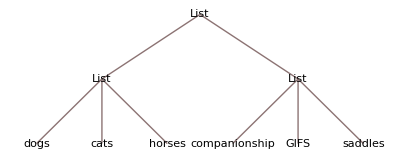

```mathematica
TreeForm[{
{"dogs","cats","horses"},
{"companionship","GIFS","saddles"}
}]
```

## Loops

In general, the standard loop functions (Do and For) should be avoided in the Wolfram Language. Due to the nature of the underlying Wolfram Language, and some implementation details, looping functions are poorly optimised compared to Map, Table and other functional operations.

However, it is perfectly acceptable to use these functions - you should use whatever programming style works best for you.

Many problems appear to be most easily specifiable in terms of loops, the following is a standard exercise for calculating the number of coin tosses required to produce 10 heads using a For loop:

```mathematica
headCount=0;
tailsCount=0;
For[i=1,
headCount<10,
i++,
If[RandomInteger[]==1,
headCount++,
tailsCount++]
];
<|"Heads"->headCount,"Tails"->tailsCount,"Tosses"->i|>
```

<|Heads→10,Tails→3,Tosses→14|>

A cleaner and (often) more efficient way to write this in a procedural manner, is with a While loop. Note that the following example is noticeably faster for large simulations as there is no iterator to update and it is possible to calculate the number of iterations in the loop implicitly from summing the headCount and tailsCount.

```mathematica
headCount=0;
tailsCount=0;
While[headCount<10,
If[RandomInteger[]==1,
headCount++,
tailsCount++];
];
<|"Heads"->headCount,"Tails"->tailsCount,"Tosses"->headCount+tailsCount|>
```

Of course, the Wolfram Language provides tools to analytically study such systems:

```mathematica
heads[n_]:=BinomialDistribution[n,1/2];
Probability[x==10,x\[Distributed]heads[n]]
```

Piecewise[{{2^-n Binomial[n,10], 10≤n}, {0, True}}]

There are a variety of built-in parametric and stochastic processes built into the language for performing these kind of simulations:

```mathematica
coinFlips=RandomFunction[BernoulliProcess[1/2],{0,30}];
ListPlot[coinFlips,Filling->Axis]
```

# Scoping Variables

In the Wolfram Language, all variables are defined globally unless specified otherwise. Whilst writing the training pack the global context became very polluted:

```mathematica
Names["Global`*"]//Short
```

{a,aball,age,assocs,«147»,σ$128498$$,σ$$,τ,$FullVersion}

Symbol and function definitions made as follows are defined globally (by default):

```mathematica
mySymbol=5;
myFunction[x_String]/;StringLength[x]<10:="short string: "<>x
```

Functions like Table, Do and For utilise what is known as dynamic scoping to define symbols local to that function call. In the example below, the global definition of i is set as 1000 but does not affect the operation of the Table call:

```mathematica
i=1000;
list=Table[i,{i,1,5}];
{i,list}
```

{1000,{1,2,3,4,5}}

In many languages, including R, functions automatically scope their variables - but this does not happen in the Wolfram Language.

```mathematica
myFunction[a_,b_]:=(
list1=RandomReal[a,b];
list2=RandomInteger[a,b];
MapThread[#1*#2&,{list1,list2}]
)
```

The symbols list1 and list2 have been defined globally rather than within the context of the function myFunction.

There are multiple potential issues with definitions being global by default:

Symbol values may change multiple times during a WL script, with unintended consequences

Data structures are stored in your working memory (RAM) and may make Mathematica unusuable or crash if extremely large intermediatetry results are stored in memory.

## Deliberate Scoping

For our purposes we shall define two types of variable scoping as follows:

Dynamic scoping: a symbol’s definition is temporarily modified within the scope of a function call and global definitions are redefined afterwards.

```mathematica
standardNamedVariable=1;
Block[{standardNamedVariable},standardNamedVariable+1]
```

Lexical scoping: a duplicate of the original symbol is made against a new, potentially temporary variable.

```mathematica
standardNamedVariable=1;
Module[{standardNamedVariable},standardNamedVariable+1]
```

Note Module is designed to perform garbage collection - deleting temporary variables after evaluation - however this is not performed with 100% efficiency. 

In general it is advised to select Block over Module to prevent garbage collection issues, there are also some significant speed advantages to using Block.

It is beyond the scope of this course, but it is useful to consult the documentation for the function With where it is necessary to overcome Hold* attributes.

# Exercises

## Simulations

In the lecture notes a coin toss was simulated and only the number of heads was recorded:

```mathematica
headCount=0;
tailsCount=0;
While[headCount<10,
If[RandomInteger[]==1,
headCount++,
tailsCount++]
];
<|"Heads"->headCount,"Tails"->tailsCount,"Tosses"->headCount+tailsCount|>
```

<|Heads→10,Tails→7,Tosses→17|>

The code needs to be modified such that the simulation run values can be returned.

Compare the difference between Append and AppendTo in this example

```mathematica
list={1,2,3};
Append[list,4]
```

```mathematica
list2={5,6,7};
AppendTo[list2,8]
```

Modify the While loop such that the simulation results are continuously appended to a variable, simulation

```mathematica
headCount=0;
While[headCount<10,
flip=RandomInteger[];
simulation=Append[simulation,flip];
If[flip==1,
headCount++]
];
simulation
```

Note that for large expressions and simulations with many iterations, it is inefficient to use Append or AppendTo. You’re advised to read the documentation for Reap and Sow where speed becomes a concern.

## propertyGrid

It is tremendously useful to quickly extract properties from the objects outputted from analytical functions in the Wolfram Language, for instance:

```mathematica
ttest=TTest[{{13,10,10,11,4},{12,5,4,5,2}},Automatic,"HypothesisTestData"];
propertyGrid[ttest]
```

DegreesOfFreedom | 8
HypothesisTestData | HypothesisTestData[…]
PValue | 0.115077
PValueTable |  | P-Value
T | 0.115077
ShortTestConclusion | Do not reject
T | 0.115077
TestConclusion | The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.
TestData | {1.76777,0.115077}
TestDataTable |  | Statistic | P-Value
T | 1.76777 | 0.115077
TestEntries | {1.76777,0.115077}
TestStatistic | 1.76777
TestStatisticTable |  | Statistic
T | 1.76777

Create the outline of a function that will output the properties of an object in a Grid, use Block to store the properties list

Use an appropriate expression generating function (Map, Table, etc) to output a list of lists from your function

Use Grid in your function to display the properties attractively

Ensure that the property Properties is not included in your grid.

Consider how you might restrict the function to work only for those objects with properties - note that this could be implemented in many different ways.

```mathematica
propertyGrid[object_]:=Block[
{
props=object["Properties"]
},
Grid[Map[{#,object[#]}&,DeleteCases[props,"Properties"]],Frame->All]
]
```

```mathematica
propertyGrid[ttest]
```

DegreesOfFreedom | 8
HypothesisTestData | HypothesisTestData[…]
PValue | 0.115077
PValueTable |  | P-Value
T | 0.115077
ShortTestConclusion | Do not reject
T | 0.115077
TestConclusion | The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.
TestData | {1.76777,0.115077}
TestDataTable |  | Statistic | P-Value
T | 1.76777 | 0.115077
TestEntries | {1.76777,0.115077}
TestStatistic | 1.76777
TestStatisticTable |  | Statistic
T | 1.76777

## DelayedRules

Previously when introducing replacement rules, elements were simply replaced based on their value:

```mathematica
{1,2,4,5}/.a_/;EvenQ[a]->"even"
```

{1,even,even,5}

RuleDelayed (:>) allows for the value of the matched expression to be manipulated through dynamic scoping:

```mathematica
{1,2,4,5}/.a_/;EvenQ[a]:>ToString[a]<>" is even"
```

{1,2 is even,4 is even,5}

Such rules can be used wherever pattern matching is used; Cases, ReplaceAll and more.

A typical example of where DelayedRules are useful is data wrangling/correction tasks, consider the following dataset:

```mathematica
desktopItems$Import=Import["https://docs.google.com/spreadsheets/d/1dYg-w-k0upVEKhBzXCbikDN33o3pMtjPhy7Zb9E7kDg/pub?gid=651658206&single=true&output=xlsx",{"XLSX","Data",1}];
```

```mathematica
desktopItems$Headers=First[desktopItems$Import];
desktopItems$Data=Rest[desktopItems$Import];
```

Use AssociationThread to create a list of Associations

```mathematica
desktopAssoc=Map[AssociationThread[desktopItems$Headers->#]&,desktopItems$Data];
```

```mathematica
desktopAssoc
```

Extract all values for the key “How many items are there on your desktop?” - do you see a mistake in the data?

Refer to the documentation for StringCases and/or RegularExpression to extract the non-digit characters from this string:

```mathematica
targetString="34343Manipulate[x,{x,{a,b,c,d}}]34334";
```

The resultant expression will be a list of strings - use StringJoin to combine the strings into one string

Wrap the function in ToExpression - what does this achieve

```mathematica
output=StringCases[targetString,RegularExpression["[^0-9]"]]
```

```mathematica
ToExpression[StringJoin@output]
```

Use ReplaceAll with RuleDelayed to correct the faulty data in the list of associations you created in question 1 - taking into account what you learned from step 3.